```mathematica
(*   
1)    F=ma
 *)
```

```mathematica
(*   
2)populacionna dinamika - zadacha na Koshi
	dx/dt = r*x, x(0) = x0 - zakon na Maltus
 *)
X[t_] = Exp[r*t] * C
```

C ⅇ^(r t)

```mathematica
D[X[t],t]
```

C ⅇ^(r t) r

```mathematica
DSolve[Y'[t] == r*Y[t],Y[t],t]
```

DSolve::dsfun: 4 ⅇ^(0.55 t) cannot be used as a function.

DSolve[2.2 ⅇ^(0.55 t)==4 ⅇ^(0.55 t) r,4 ⅇ^(0.55 t),t]

```mathematica
(* dx/dt = r*x*(K-x) , x(0) = x0 - zakon na Werhulst*)
```

```mathematica
DSolve[{G'[t] == r*G[t]*(K-G[t]), G[0] == x0}, G[t], t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{G[t]→(ⅇ^(K r t) K x0)/(K-x0+ⅇ^(K r t) x0)}}

```mathematica
{{G[t]->(ⅇ^(K r t) K x0)/(K-x0+ⅇ^(K r t) x0)}}
```

{{G[t]→(ⅇ^(K r t) K x0)/(K-x0+ⅇ^(K r t) x0)}}

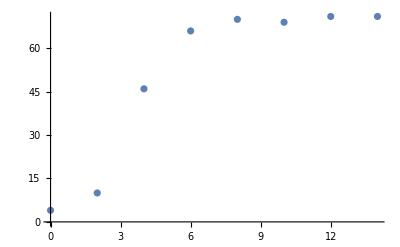

```mathematica
ListPlot[Transpose[{{0,2,4,6,8,10,12,14},{4,10,46,66,70,69,71,71}}]]
```

```mathematica
X[t_] = x0*Exp[r*t]
```

ⅇ^(r t) x0

```mathematica
Y[t_] = 4*Exp[0.55*t]
```

4 ⅇ^(0.55 t)

```mathematica
Clear[X]
```

```mathematica
plot1 = ListPlot[Transpose[{{0,2,4,6,8,10,12,14},{4,10,46,66,70,69,71,71}}]]
```

-Graphics-

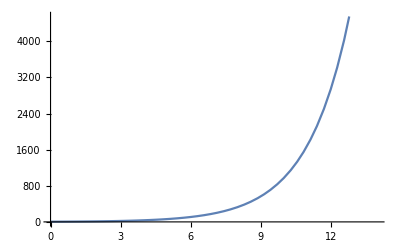

```mathematica
plot2=Plot[Y[t],{t,0,14}] (* Maltus *)
```

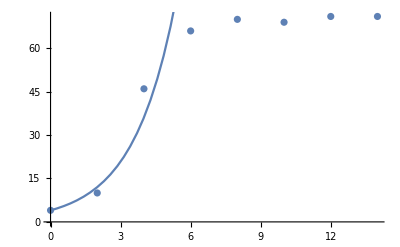

```mathematica
Show[plot1,plot2]
```

```mathematica
X[t_] = (71*4*Exp[71*0.012*t])/(71+4*(Exp[71*0.012*t] - 1))
```

(284 ⅇ^(0.852 t))/(71+4 (-1+ⅇ^(0.852 t)))

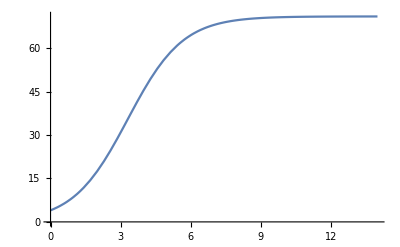

```mathematica
plot2 = Plot[X[t], {t, 0, 14}] (*furhulst*)
```

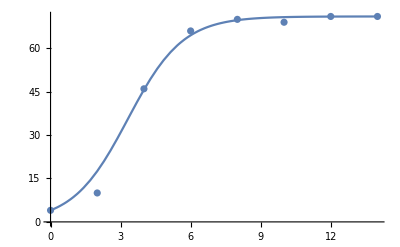

```mathematica
Show[plot1,plot2]
```

```mathematica
(* 
priblijavane na proizvodna 
f'(t) = lim (f(t+Delta(t))-f(t))/Delta(t) 
     Delta(t)->0

na kompiutur:
1 nachin:
f'(t) ~ (f(t+Delta(t)) - f(t))/Delta(t) , Delta(t) -> malko

  2 nachin:
f'(t) ~ (f(t)-f(t-Delta(t)))/Delta(t) 

3 nachin:
f'(t) ~ (f(t+Delta(t))-f(t-Delta(t)))/2*Delta(t)
*)

(* Da se pribliji proizvodnata na f(x) = e^x v [0,10] kato se izpolzvat (1)(2) i (3). Da se nachertaqt na edna grafika proizvodnata i nejnite pribl. pri 
Delta(t) = 0.5, 
Delta(t) = 0.001,Delta(t) = 10^=15. *)
```

```mathematica
F[t_] = Exp[t]
DerF1[t_,dt_] = (F[t + dt] - F[t])/dt
```

ⅇ^t

(-ⅇ^t+ⅇ^(dt+t))/dt

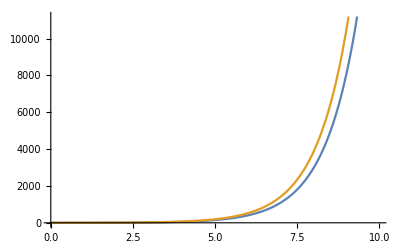

```mathematica
Plot[{F[t],DerF1[t,0.5]},{t,0,10}] (* (1) *)
```

ⅇ^t-100 (-ⅇ^t+ⅇ^(1/100+t))

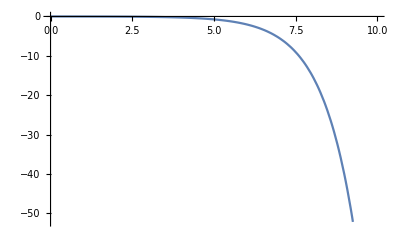

```mathematica
Ea1[h_] = F[t] - DerF1[t,h]
Plot[Ea1[0.5],{t,0,10}]
```

```mathematica
Er1[h_] = Ea1[h] / F[t]
```

ⅇ^-t (ⅇ^t-100 (-ⅇ^t+ⅇ^(1/100+t)))

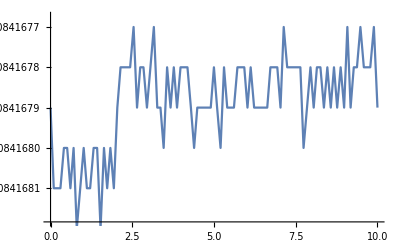

```mathematica
Plot[Er1[0.5],{t,0,10}]
```

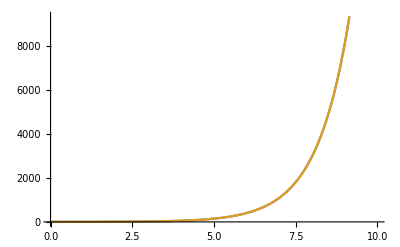

```mathematica
Plot[{F[t],DerF1[t,0.001]},{t,0,10}]
```

```mathematica
Plot[Ea1[0.001],{t,0,10}]
```

-Graphics-

```mathematica
Plot[Er1[0.001],{t,0,10}]
```

-Graphics-

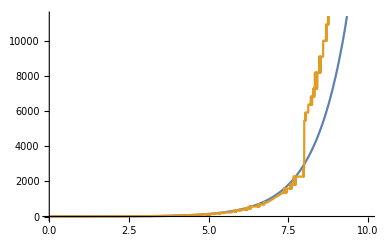

```mathematica
Plot[{F[t],DerF1[t,10^(-15)]},{t,0,10}]
```

```mathematica
Plot[Ea1[10^(-15)],{t,0,10}]
```

-Graphics-

```mathematica
Plot[Er1[10^(-15)],{t,0,10}]
```

-Graphics-

```mathematica
DerF2[t_, dt_] = (F[t]-F[t-dt])/dt (* (2) *)
```

(ⅇ^t-ⅇ^(-dt+t))/dt

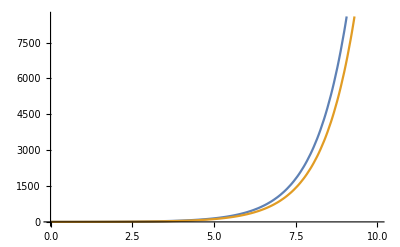

```mathematica
Plot[{F[t], DerF2[t,0.5]},{t,0,10}]
```

```mathematica
Ea2[h_] = F[t] - DerF2[t,h]
Er2[h_] = Ea2[h] / F[t]
```

ⅇ^t-100 (-ⅇ^(-1/100+t)+ⅇ^t)

ⅇ^-t (ⅇ^t-100 (-ⅇ^(-1/100+t)+ⅇ^t))

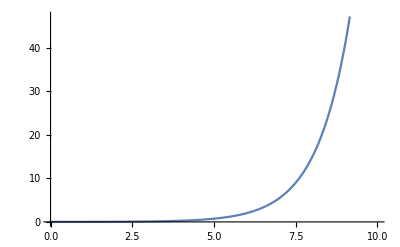

```mathematica
Plot[Ea2[0.5],{t,0,10}]
```

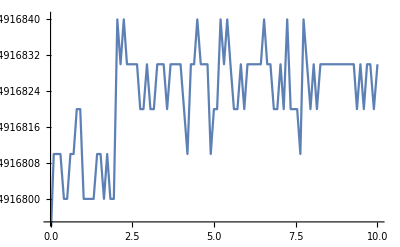

```mathematica
Plot[Er2[0.5],{t,0,10}]
```

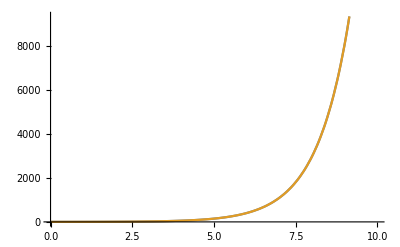

```mathematica
Plot[{E^t, DerF2[t, 0.001]}, {t,0,10}]
```

```mathematica
Plot[Ea2[0.001],{t,0,10}]
```

-Graphics-

```mathematica
Plot[Er2[0.001],{t,0,10}]
```

-Graphics-

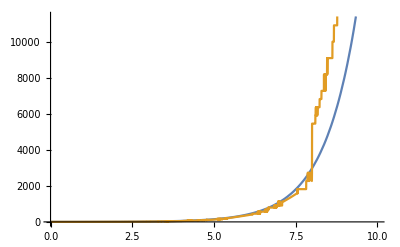

```mathematica
Plot[{E^t, DerF2[t, 10^(-15)]}, {t,0,10}]
```

```mathematica
Plot[Ea2[10^(-15)],{t,0,10}]
```

-Graphics-

```mathematica
Plot[Er2[10^(-15)],{t,0,10}]
```

-Graphics-

```mathematica
DerF3[t_, dt_] = (F[t+dt] - F[t-dt])/(2*dt) (* (3) *)
```

(-ⅇ^(-dt+t)+ⅇ^(dt+t))/(2 dt)

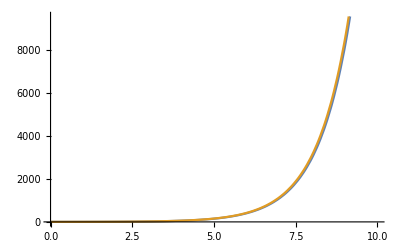

```mathematica
Plot[{E^t, DerF3[t, 0.5]}, {t,0,10}]
```

```mathematica
Ea3[h_] = F[t] - DerF3[t,h]
Er3[h_] = Ea3[h]/F[t]
```

ⅇ^t-50 (-ⅇ^(-1/100+t)+ⅇ^(1/100+t))

ⅇ^-t (ⅇ^t-50 (-ⅇ^(-1/100+t)+ⅇ^(1/100+t)))

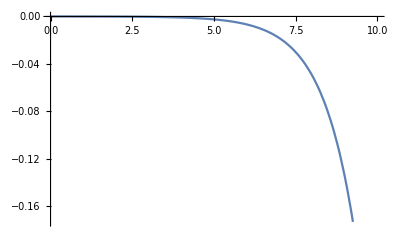

```mathematica
Plot[Ea3[0.5],{t,0,10}]
```

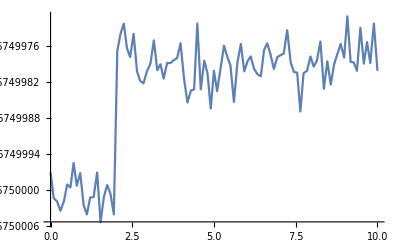

```mathematica
Plot[Er3[0.5],{t,0,10}]
```

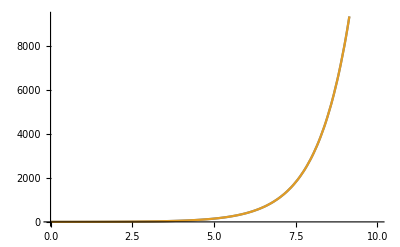

```mathematica
Plot[{E^t, DerF3[t,0.001]}, {t,0,10}]
```

```mathematica
Plot[Ea3[0.001],{t,0,10}]
```

-Graphics-

```mathematica
Plot[Er3[0.001],{t,0,10}]
```

-Graphics-

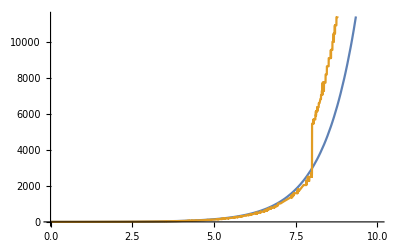

```mathematica
Plot[{E^t, DerF3[t,10^(-15)]}, {t,0,10}]
```

```mathematica
Plot[Ea3[10^(-15)],{t,0,10}]
```

-Graphics-

```mathematica
Plot[Er3[10^(-15)],{t,0,10}]
```

-Graphics-

```mathematica
(* ----------------------------------------------- *)
a = 5
```

5

```mathematica
If[a == 5, "T", "F"]
```

T

```mathematica
For[i = 1, i≤ 10, i++,
Print[i^2]
]
```

1

4

9

16

25

36

49

64

81

100

```mathematica
list = {1,2,3}
```

{1,2,3}

```mathematica
G[A_, B_] := (
AppendTo[list,A];
Print[B^2];
)
```

```mathematica
G[1,2]
```

4

```mathematica
list
```

{1,2,3,1}

```mathematica
(* Da se pribliji funkciqta sin(x)*cos(x)*x v [0,10] s polinom na Teilur ot stepen 2,3,4. *)
```

```mathematica
F2[x_] := Sin[x]*Cos[x]*x
Taylor[x_,x0_, p_] := F2[x0] + Sum[ ( (D[F2[y], {y,i}]/.y->x0)*((x-x0)^i))/i!,{i,1,p}]
```

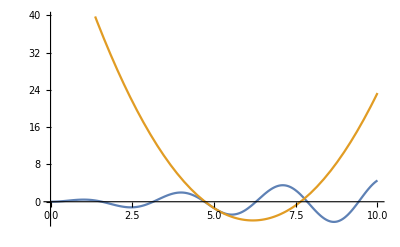

```mathematica
Plot[{F2[x],Taylor[x,5,2]}, {x,0,10}]
```

```mathematica
Clear[Ea]
```

```mathematica
Ea[i_] = F2[x] - Taylor[x,5,i];
```

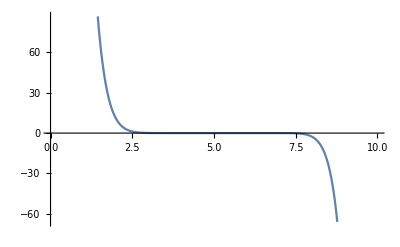

```mathematica
Plot[Ea[2],{x,0,10}]
```

```mathematica
Er[i_] = Ea[i]/F2[x];
```

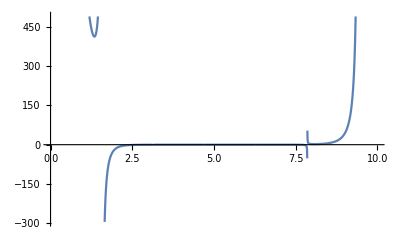

```mathematica
Plot[Er[2],{x,0,10}]
```

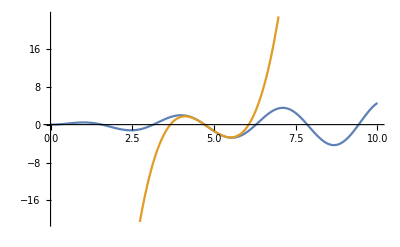

```mathematica
Plot[{F2[x],Taylor[x,5,3]}, {x,0,10}]
```

```mathematica
Plot[Ea[3],{x,0,10}]
```

-Graphics-

```mathematica
Plot[Er[3],{x,0,10}]
```

-Graphics-

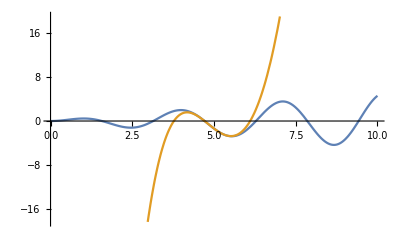

```mathematica
Plot[{F2[x],Taylor[x,5,4]}, {x,0,10}]
```

```mathematica
Plot[Ea[4],{x,0,10}]
```

-Graphics-

```mathematica
Plot[Er[4],{x,0,10}]
```

-Graphics-

```mathematica
(* 
Задача на Коши.Явен метод на Ойлер.
По явния и неявния метод на Ойлер да се реши моделната задача
u'(x)=-10u, 0<x≤1
u(0)=1
при n=4,20,100. Да се изобразят графично на един чертеж точното и приближеното решение.
*)
```

```mathematica
ExplicitEuler[n_, u0_,t0_,T_] := (
h = (T-t0)/n;
tList = Table[ t0 + i*h ,{i,0,n}]; 
yList = Table[u0, {i,0,n}];
yList[[1]] = 1;
f[u_] := -10*u;
For[i=2,i≤n+1,i++,
yList[[i]] = yList[[i-1]] + h*f[yList[[i-1]]]];
Transpose[{tList,yList}]
)
```

```mathematica
sol = DSolve[{u'[x] == -10u[x], u[0] == 1}, u[x], x];
```

```mathematica
exact[x_] = sol[[1,1,2]]
```

ⅇ^(-10 x)

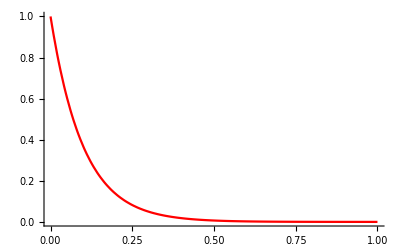

```mathematica
plotExact = Plot[exact[x],{x,0,1}, PlotRange -> All, PlotStyle -> Red]
```

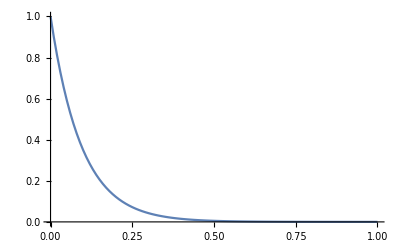

```mathematica
plotAppr = ListLinePlot[ExplicitEuler[100,1,0,1], PlotRange -> All] (* n=4 *)
```

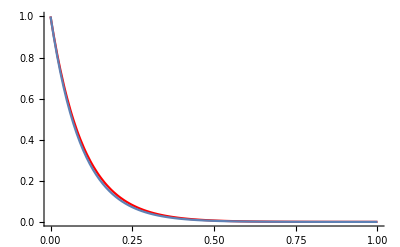

```mathematica
Show[plotExact, plotAppr, PlotRange -> All]
```

```mathematica
Manipulate[
Show[plotExact,
ListLinePlot[ExplicitEuler[n,1,0,1], PlotRange -> {{0,1}, {-2,2}}]] ,
{n,4,100,1}]
```

```mathematica
FindRoot[0 == Sin[x], {x,10}]
```

{x→9.42478}

```mathematica
ImplicitEuler[n_, u0_,t0_,T_] := ( (*neqven metod na oiler *)
h = (T-t0)/n;
tList = Table[ t0 + i*h ,{i,0,n}]; 
yList = Table[u0, {i,0,n}];
yList[[1]] = 1;
f[u_] := -10*u;
For[i=2,i≤n+1,i++,
yList[[i]] = FindRoot[yi==yList[[i-1]] + h*f[yi],{yi,yList[[i]] = yList[[i-1]] + h*f[yList[[i-1]]]}][[1,2]]];
Transpose[{tList,yList}]
)
```

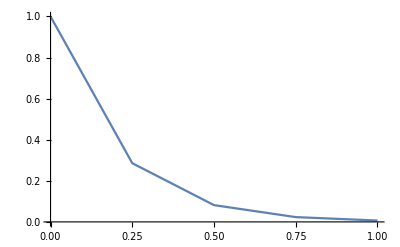

```mathematica
plotAppr = ListLinePlot[ImplicitEuler[4,1,0,1]]
```

```mathematica
Manipulate[
Show[plotExact,
ListLinePlot[ImplicitEuler[n,1,0,1], PlotRange -> {{0,1}, {-2,2}}]] ,
{n,4,100,1}]
```